# Verify muralizer algorithm on the arduino

## Inverse transformation (to check results)

```mathematica
inversexform[refpoints_]:=Function[{radii},
Block[{ra=radii⟦1⟧,rb=radii⟦2⟧,xa=refpoints⟦1,1⟧,ya=refpoints⟦1,2⟧,xb=refpoints⟦2,1⟧,yb=refpoints⟦2,2⟧},
{(xa+xb)/2+((ra-rb) (ra+rb) (-xa+xb))/(2 ((-xa+xb)^2+(-ya+yb)^2))+((-ya+yb) √(-(-(ra-rb)^2+(-xa+xb)^2+(-ya+yb)^2) (-(ra+rb)^2+(-xa+xb)^2+(-ya+yb)^2)))/(2 ((-xa+xb)^2+(-ya+yb)^2)),(ya+yb)/2+((ra-rb) (ra+rb) (-ya+yb))/(2 ((-xa+xb)^2+(-ya+yb)^2))-((-xa+xb) √(-(-(ra-rb)^2+(-xa+xb)^2+(-ya+yb)^2) (-(ra+rb)^2+(-xa+xb)^2+(-ya+yb)^2)))/(2 ((-xa+xb)^2+(-ya+yb)^2))}
]
]
```

## Set directory

```mathematica
SetDirectory["/data/noisebridge/muralizer/"]
FileNames[]
```

/data/noisebridge/muralizer

{AngularAcceleration.nb,AngularAcceleration.pdf,ArduinoAlgorithmVerify.nb,ArduinoAlgorithmVerify.pdf,arduinolog,bitbucket,foo.ps.gz,GeckoTester.jpg,ImplicitMuralizerLine.nb,ImplicitMuralizerLine.pdf,MuralizerCoordinates.nb,MuralizerCoordinates.pdf,referencedata.m,RunningOnMurals.nb,RunningOnMurals.pdf,scratch.nb,.svn,Van_Aken_Paper.pdf}

## Mathematica output

```mathematica
mathematicapath=Import["referencedata.m"];
Dimensions[mathematicapath]
```

{17982,2}

## arduino output

```mathematica
arduinoraw=Import["arduinolog","Table"];
Dimensions[arduinoraw]
```

{43161}

```mathematica
arduinopath=Prepend[Drop[#,2],First[#]]&[ToExpression[StringReplace[#,{"("->"{",")"->"}"}]]&/@Select[First/@Select[arduinoraw,Length[#]==1&],MatchQ[#,s_String/;StringMatchQ[s,"(*,*)*"]]&]];
Dimensions[arduinopath]
```

{17982,2}

## Comparison

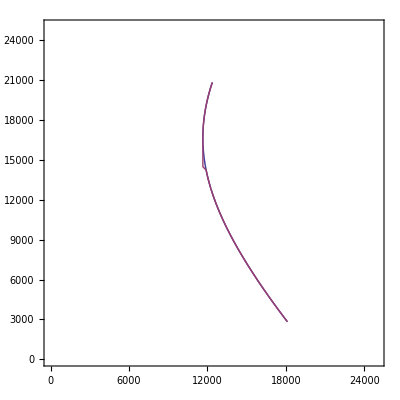

```mathematica
ListPlot[{mathematicapath,arduinopath},Joined->True,Frame->True,PlotRange->{#,#}&[{0,25000}],AspectRatio->1]
```

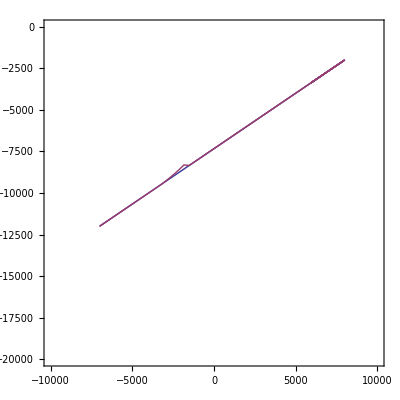

```mathematica
ListPlot[inversexform[{{-10000,0},{10000,0}}]/@#&/@{mathematicapath,arduinopath},Joined->True,Frame->True,PlotRange->{{-10000,10000},{-20000,0}},AspectRatio->1]
```

```mathematica
pathdiff=arduinopath-mathematicapath;
Dimensions[pathdiff]
```

{17982,2}

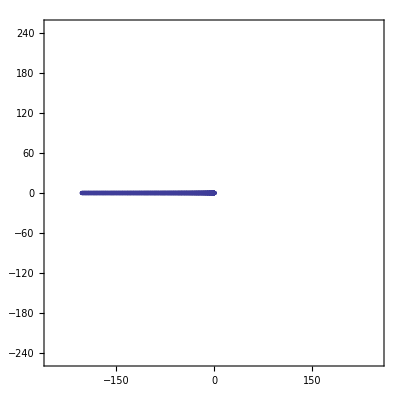

```mathematica
ListPlot[pathdiff,Frame->True,PlotRange->{{-1,1},{-1,1}}250,AspectRatio->1]
```

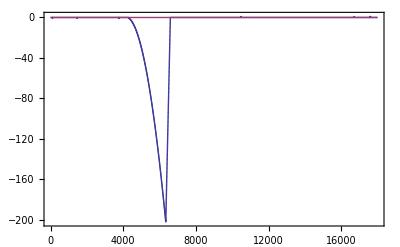

```mathematica
ListPlot[Transpose[pathdiff],Joined->True,Frame->True]
```